## Lagrangian

```mathematica
Quit[]
```

```mathematica
ClearAll["Global`*"]
```

### ODEs

#### No contact

```mathematica
RodOde[R:{__?NumericQ}]:=Block[
{Sol,S,s,nx,ny,x,y,θ,m},
Sol=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S]*(x[S]-px[S]),
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x[S],y[S],θ[S],s[S],nx[S],ny[S],m[S]},{S,0,L/2}][[1]];
{x[S]-L/2,y[S],θ[S]}/.Sol/.S->L/2
];

EquilSol[R_]:=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S]),
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x,y,θ,S,m,nx,ny},{S,0,L/2}][[1]];
```

```mathematica
(* With repulsion *)
RodOdeRepulsion[R:{__?NumericQ}]:=Block[
{Sol,S,s,nx,ny,x,y,θ,m},
Sol=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S]*(x[S]-px[S]) + γ[S]*Q/(x[S] - L/2*1.01)^n*HeavisideTheta[L/2-x[S]],
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x[S],y[S],θ[S],s[S],nx[S],ny[S],m[S]},{S,0,L/2}][[1]];
{x[S]-L/2,y[S],θ[S]}/.Sol/.S->L/2
];

EquilSolRepulsion[R_]:=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S])+ γ[S]*Q/(x[S] - L/2*1.01)^n*HeavisideTheta[L/2-x[S]],
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x,y,θ,S,m,nx,ny},{S,0,L/2}][[1]];
```

#### 1 Contact point

```mathematica
RodOdeContactPt[R:{__?NumericQ}]:=Block[
{Sol,Cond},
Sol=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S])-R[[5]]DiracDelta[S-R[[4]]],
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x[S],y[S],θ[S],s[S],nx[S],ny[S],m[S]},{S,0,L/2}][[1]];

Cond = {x[S]-δ,θ[S]+π/2}/.Sol/.S->R[[4]];

AppendTo[Cond,{x[S]-L/2,y[S],θ[S]}/.Sol/.S->L/2];
Flatten[Cond]
];
EquilSolnContactPt[R_]:=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S])-R[[5]]DiracDelta[S-R[[4]]],
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x,y,θ,s,nx,ny,m},{S,0,L/2}][[1]];
```

```mathematica
(* With repulsion *)
RodOdeContactPtRepulsion[R:{__?NumericQ}]:=Block[
{Sol,Cond},
Sol=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S])-R[[5]]DiracDelta[S-R[[4]]]+ γ[S]*Q/(x[S] - L/2*1.01)^n*HeavisideTheta[L/2-x[S]],
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x[S],y[S],θ[S],s[S],nx[S],ny[S],m[S]},{S,0,L/2}][[1]];

Cond = {x[S]-δ,θ[S]+π/2}/.Sol/.S->R[[4]];

AppendTo[Cond,{x[S]-L/2,y[S],θ[S]}/.Sol/.S->L/2];
Flatten[Cond]
];
EquilSolnContactPtRepulsion[R_]:=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S])-R[[5]]DiracDelta[S-R[[4]]]+ γ[S]*Q/(x[S] - L/2*1.01)^n*HeavisideTheta[L/2-x[S]],
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x,y,θ,s,nx,ny,m},{S,0,L/2}][[1]];
```

#### 1 Contact point, with area constraint

```mathematica
RodOdeContactPtAreaCons[R:{__?NumericQ}]:=Block[
{Sol,Cond},
(* R = {nx[0], y[0], m[0], sc, f - contact force, p - lagrange multiplier for area constraint *)
Sol=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S])-R[[5]]DiracDelta[S-R[[4]]]+R[[6]] Sin[θ[S]]UnitStep[R[[4]]-S],
ny'[S]==k γ[S](y[S]-py[S])-R[[6]]Cos[θ[S]]UnitStep[R[[4]]-S],
A'[S]==-x[S]γ[S]Sin[θ[S]],
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],A[0]==0,θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x[S],y[S],A[S],θ[S],s[S],nx[S],ny[S],m[S]},{S,0,L/2}][[1]];

Cond = {x[S]-δ,θ[S]+π/2,A[S]-A0}/.Sol/.S->R[[4]];

AppendTo[Cond,{x[S]-L/2,y[S],θ[S]}/.Sol/.S->L/2];
Flatten[Cond]
];


EquilSolnContactPtAreaCons[R_]:=
NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S])-R[[5]]DiracDelta[S-R[[4]]]+R[[6]] Sin[θ[S]]UnitStep[R[[4]]-S],
ny'[S]==k γ[S](y[S]-py[S])-R[[6]]Cos[θ[S]]UnitStep[R[[4]]-S],
A'[S]==-x[S]γ[S]Sin[θ[S]],
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],A[0]==0,θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x,y,θ,s,A,nx,ny,m},{S,0,L/2}][[1]];
```

#### Contact region

```mathematica
RodOdeContactRegion[R:{__?NumericQ}]:=Block[
{Sol,Cond,S1,S2,f,S},
(* R = {nx[0], y[0], m[0], S1, S2, f, p } *)

S1=R[[4]];
S2=R[[5]];
f=R[[6]];

(* fixed area region; pre-contact *)
Sol=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S])+p Sin[θ[S]]UnitStep[S1-S]-f UnitStep[S-S1]UnitStep[S2-S],
ny'[S]==k γ[S](y[S]-py[S])-p Cos[θ[S]]UnitStep[S1-S],
A'[S]==-x[S]γ[S]Sin[θ[S]],
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]])(UnitStep[S1-S]+UnitStep[S-S2]),
x[0]==0,y[0]==R[[2]],A[0]==0,θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x[S],y[S],θ[S],A[S],s[S],nx[S],ny[S],m[S]},{S,0,L/2}][[1]];

Cond = {x[S]-δ,θ[S]+π/2,m[S],A[S]-A0}/.Sol/.S->S1;
AppendTo[Cond,{x[S]-L/2,y[S],θ[S]}/.Sol/.S->L/2];
Flatten[Cond]
];


EquilSolContactRegion[R_]:=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S])+R[[7]] Sin[θ[S]]UnitStep[R[[4]]-S]-R[[6]] UnitStep[S-R[[4]]]UnitStep[R[[5]]-S],
ny'[S]==k γ[S](y[S]-py[S])-R[[7]] Cos[θ[S]]UnitStep[R[[4]]-S],
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]])(UnitStep[R[[4]]-S]+UnitStep[S-R[[5]]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x,y,s,θ,m,nx,ny},{S,0,L/2}][[1]];
```

```mathematica
(* Repulsion *)
RodOdeContactRegionRepulsion[R:{__?NumericQ}]:=Block[
{Sol,Cond,S1,S2,f,S},
(* R = {nx[0], y[0], m[0], S1, S2, f, p } *)

S1=R[[4]];
S2=R[[5]];
f=R[[6]];

(* fixed area region; pre-contact *)
Sol=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S])+ γ[S]*Q/(x[S] - L/2*1.01)^n*HeavisideTheta[L/2-x[S]]-f UnitStep[S-S1]UnitStep[S2-S],
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]])(UnitStep[S1-S]+UnitStep[S-S2]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x[S],y[S],θ[S],s[S],nx[S],ny[S],m[S]},{S,0,L/2}][[1]];

Cond = {x[S]-δ,θ[S]+π/2,m[S]}/.Sol/.S->S1;
AppendTo[Cond,{x[S]-L/2,y[S],θ[S]}/.Sol/.S->L/2];
Flatten[Cond]
];


EquilSolContactRegionRepulsion[R_]:=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S])+ γ[S]*Q/(x[S] - L/2*1.01)^n*HeavisideTheta[L/2-x[S]]-R[[6]] UnitStep[S-R[[4]]]UnitStep[R[[5]]-S],
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]])(UnitStep[R[[4]]-S]+UnitStep[S-R[[5]]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x,y,s,θ,m,nx,ny},{S,0,L/2}][[1]];
```

### Heterogeneous stiffness, uniform growth

#### Initial solution, parameters

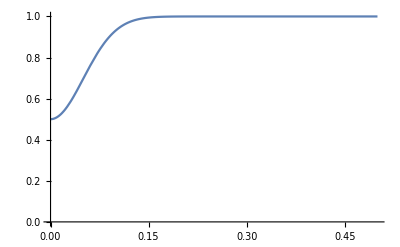

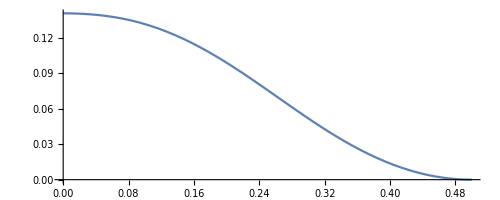

```mathematica
Clear[γ,R,Sol,sol,EB,px,py];
(* parameters *)
k=50;
dt=0.05;
dth = dt; (* initialising successful step size *)
δ=0.02;
L=1;
η=1;
γ[S_]=1+dt;
px[S_]:=S;
py[S_]:=0;
EB[s_]:=1-.5Exp[-s^2/(.005)];
Sol=FindRoot[RodOde[R],{R,{-42,0.1,-4}}];
Plot[EB[s],{s,0,1/2},PlotRange->{0,1}]
ParametricPlot[Evaluate[{x[S],y[S]}/.EquilSol[R/.Sol]],{S,0,L/2}]
```

#### Growth to contact

```mathematica
grs={};
(* first step *)
g=1+dt;
γ[S_]=g;
Sol=FindRoot[RodOde[R],{R,R/.Sol}];
sol=EquilSol[R/.Sol];
rs=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];

(* second step *)
g=g+dt;
γ[s_]=g;
Sol=FindRoot[RodOde[R],{R,R/.Sol}];
sol=EquilSol[R/.Sol];
re=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];

(* tracing *)
flag=0;
FailCount=0;
TOL=10^-6;
MaxDt=0.35;
MaxFails=60;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];
P2=Plot[(x[S]-δ)/.sol,{S,0,L/2}];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
J2 = CreateWindow[DocumentNotebook[P2],WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)
rd
While[flag==0,
t = (re - rs);
g=g+dt;
γ[s_]=g;
Sol=Quiet[Reap[FindRoot[RodOde[R],{R,re+dt/dth*t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOde[R/.Sol[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
g=g-dt;
γ[s_]=g;
dt = 0.5 dt; Print[dt];If[FailCount == MaxFails, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSol[R/.Sol[[1]]];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];

Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];
P2=Plot[(x[S]-δ)/.sol,{S,0,L/2}];
CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 CreateWindow[DocumentNotebook[P2],J2,WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];
(*FinishDynamic[]*);

(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

rd

0.0625

0.078125

0.0976563

0.12207

0.152588

0.0762939

0.038147

0.0190735

0.0238419

0.0298023

0.0372529

0.0465661

0.0232831

0.0116415

0.00582077

0.00727596

0.00909495

0.00454747

0.00227374

0.00284217

0.00355271

0.00444089

0.00555112

0.00693889

0.00867362

0.010842

0.0135525

0.00677626

0.00847033

0.0105879

0.0132349

0.0165436

0.0206795

0.0103398

0.00516988

0.00646235

0.00323117

0.00161559

0.00201948

0.00252435

0.00315544

0.0039443

0.00493038

0.00616298

0.00770372

0.00962965

0.0120371

0.0150463

0.0188079

0.0235099

0.0293874

0.0367342

0.0459177

0.0229589

0.0114794

0.0143493

0.00717465

0.00896831

0.0112104

0.014013

0.00700649

0.00875812

0.00437906

0.00547382

0.00684228

0.00342114

0.00171057

0.00213821

0.00267276

0.00133638

0.00167048

0.000835239

0.00104405

0.00130506

0.00163133

0.000815663

0.000407832

0.000509789

0.000637237

0.000796546

0.000995682

0.0012446

0.00155575

0.000777877

0.000388938

0.000486173

0.000607716

0.000303858

0.000151929

0.000189911

0.0000949557

0.0000474778

0.0000237389

0.0000118695

0.0000148368

7.41841×10^-6

3.70921×10^-6

1.8546×10^-6

2.31825×10^-6

2.89782×10^-6

3.62227×10^-6

1.81114×10^-6

9.05568×10^-7

4.52784×10^-7

5.6598×10^-7

7.07475×10^-7

8.84344×10^-7

4.42172×10^-7

5.52715×10^-7

6.90893×10^-7

Part::partw: Part 1 of {} does not exist.

8.63617×10^-7

4.31808×10^-7

5.39761×10^-7

6.74701×10^-7

8.43376×10^-7

$Aborted

```mathematica
NotebookClose[J1];NotebookClose[J2];
```

```mathematica
Manipulate[ParametricPlot[{x[s],y[s]}/.grs[[i,6]],{s,0,grs[[i,2]]/2},PlotRange->All],{i,1,Length[grs],1}]
```

Part::partd: Part specification grs ⟦ 27, 2 ⟧ is longer than depth of object.

ParametricPlot::plln: Limiting value 1/2\ grs ⟦ 27, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$412, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 27, 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value 1/2\ grs ⟦ 27, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$412, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 27, 2 ⟧ is longer than depth of object.

ParametricPlot::plln: Limiting value 1/2\ grs ⟦ 27, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$412, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 27, 2 ⟧ is longer than depth of object.

ParametricPlot::plln: Limiting value 1/2\ grs ⟦ 27, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$412, 2 ⟧} is not a machine-sized real number.

Part::partw: Part 27 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ParametricPlot::plln: Limiting value 1 in {s, 0, 1/2\ grs ⟦ FE`i$$1631, 2 ⟧} is not a machine-sized real number.

```mathematica
Manipulate[Plot[(x[s]-δ)/.grs[[i,6]],{s,0,L/2}],{i,1,Length[grs],1}]
```

Plot::plln: Limiting value L/2 in {s, 0, L/2} is not a machine-sized real number.

Plot::plln: Limiting value Global`L/2 in {Global`s, 0, Global`L/2} is not a machine-sized real number.

Plot::plln: Limiting value L/2 in {s, 0, L/2} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 27, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 27, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 27, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 27, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 27, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ReplaceAll::reps: {grs ⟦ 27, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 27, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 27, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 27, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 27, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 27, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ReplaceAll::reps: {grs ⟦ 27, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 27 of {1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 24 »{10.202149658203126`, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {« 9 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 27, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 27 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 24 »{10.202149658203126`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 27 of {1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 24 »{10.202149658203126`, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {« 9 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{« 1 »} ⟦ 27, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
Save[ToString[$HomeDirectory]<>"/Dropbox/Research (unshared,current)/Morphorods/SelfContact/Lagrangian", grs]
```

```mathematica
re
```

{-3.8949,1.43702,-2.99537}

```mathematica
rs
```

{-3.97944,1.42976,-3.03567}

```mathematica
dt
```

8.43376×10^-7

```mathematica
dth
```

6.74701×10^-7

#### First contact point

InterpolatingFunction::dmval: Input value {-2.1859} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

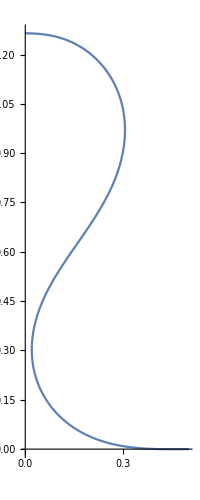

```mathematica
ii=27;
sc=0.33; (* guess for contact location *)
grs=Table[grs[[k]],{k,1,ii}];
γ[S_]=grs[[ii,1]];
R0=grs[[ii,5]];
R0=Flatten[AppendTo[R0,{sc,0}]];
px=grs[[ii,7]];
py=grs[[ii,8]];
Sol=FindRoot[RodOdeContactPt[R],{R,R0}];
sol=EquilSolnContactPt[R/.Sol];
ParametricPlot[{x[S],y[S]}/.sol,{S,0,L/2}]
```

```mathematica
A0=-NIntegrate[x[S]y'[S]/.sol,{S,0,(R/.Sol)[[4]]}]
```

0.182148

```mathematica
rs=Flatten[AppendTo[R/.Sol,0]]
```

Set::write: Tag ReplaceAll in R/. {R → {-6.02071, 1.26449, -3.74703, 0.326621, -2.12607}} is Protected.

{-6.02071,1.26449,-3.74703,0.326621,-2.12607,0}

```mathematica
Sol=FindRoot[RodOdeContactPtAreaCons[R],{R,rs}];
sol=EquilSolnContactPtAreaCons[R/.Sol];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
g=γ[s]
```

3.71982

#### Evolving contact point; Seeking contact region

```mathematica
(* first step done above *)
(*g=3.825;*)
γ[S_]=g;
rs=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* second step *)
dt=0.005;
dth=dt; (* initialising successful dt *)
g=g+dt;
γ[S_]=g;
Sol=FindRoot[RodOdeContactPtAreaCons[R],{R,R/.Sol}];
sol=EquilSolnContactPtAreaCons[R/.Sol];
re=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,re,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* tracing *)
flag=0;
FailCount=0;
TOL=10^-4;
MaxDt=0.15;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];
P2=Plot[m[S]/.sol,{S,0,L/2}];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
J2 = CreateWindow[DocumentNotebook[P2],WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)

While[flag==0,
t = (re - rs);
g=g+dt;
γ[S_]=g;

Sol=Quiet[Reap[FindRoot[RodOdeContactPtAreaCons[R],{R,re+dt/dth t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOdeContactPtAreaCons[R/.Sol[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
g=g-dt;
dt = 0.5 dt; Print[dt];If[FailCount == 100, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSolnContactPtAreaCons[ R/.Sol[[1]]];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol],{S,0,L/2}];
P2=Plot[m[S]/.sol,{S,0,L/2}];
 CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 CreateWindow[DocumentNotebook[P2],J2,WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];
(*FinishDynamic[]*)

(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

0.00625

0.0078125

0.00390625

0.00195313

0.00244141

0.00305176

0.0038147

0.00476837

0.00596046

0.00745058

0.00372529

0.00465661

0.00232831

0.00116415

0.00145519

0.00181899

0.00227374

0.00284217

0.00355271

0.00444089

0.00555112

0.00277556

0.00346945

0.00433681

0.00542101

0.00677626

0.00847033

0.0105879

0.0132349

0.0165436

0.00827181

0.0041359

0.00206795

0.00103398

0.000516988

0.000646235

0.000323117

0.000161559

0.0000807794

0.000100974

0.0000504871

0.0000252435

0.0000315544

0.0000157772

$Aborted

```mathematica
NotebookClose[J1];NotebookClose[J2];
```

```mathematica
ii=27;
```

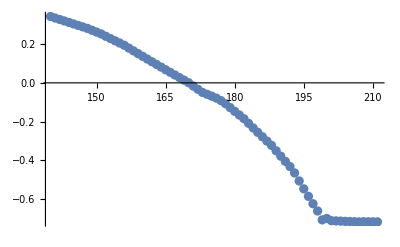

```mathematica
ListPlot[Table[{i,m[S]/.grs[[i,6]]/.S->grs[[i,5,4]]},{i,140,Length[grs]}]]
```

```mathematica
Save[ToString[$HomeDirectory]<>"/Dropbox/Research (unshared,current)/Morphorods/SelfContact/Lagrangian", grs]
```

```mathematica
grs=Get[ToString[$HomeDirectory]<>"/Dropbox/Research (unshared,current)/Morphorods/SelfContact/Lagrangian"];
```

```mathematica
rs
```

{-12.7635,1.62753,-3.8847,0.329691,29.5452,-89.9429}

```mathematica
re
```

{-12.7627,1.62759,-3.88447,0.32971,29.555,-89.9409}

```mathematica
Manipulate[ParametricPlot[{{-x[S],y[S]}/.grs[[i,6]],{x[S],y[S]}/.grs[[i,6]]},{S,0,L/2},PlotRange->All,PlotStyle->{Blue,Blue}],{i,1,Length[grs],1}]
Manipulate[Plot[m[S]/.grs[[i,6]],{S,0,L/2}],{i,1,Length[grs],1}]
```

Part::partw: Part 173 of {1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11579914359571852`, 0.21007930845062223`, 0.29986920038406517`, 0.3997266598642311`, 0.5`}}, {{0.00704715003623664`, 0.`}, {0.006354241591438223`, -0.013101676939791277`}, {0.004658135907468784`, -0.021651374946806204`}, {0.0026301532458439525`, -0.02223872562922858`}, {0.0007393483798990123`, -0.014223869549051419`}, {-2.025278648428969`*^-18, -3.179622472695829`*^-11}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}{1.1`, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {« 9 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 48 »« 103 » does not exist.

ReplaceAll::reps: {{1.05`, 1, 1 - 0.5` ⅇ^Times[« 2 »], 50, {« 1 »}, {« 1 »}, TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11579914359571852`, 0.21007930845062223`, 0.29986920038406517`, 0.3997266598642311`, 0.5`}}, {{0.00704715003623664`, 0.`}, {0.006354241591438223`, -0.013101676939791277`}, {0.004658135907468784`, -0.021651374946806204`}, {0.0026301532458439525`, -0.02223872562922858`}, {0.0007393483798990123`, -0.014223869549051419`}, {-2.025278648428969`*^-18, -3.179622472695829`*^-11}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 49 », « 103 »} ⟦ 173, 6 ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11579914359571852`, 0.21007930845062223`, 0.29986920038406517`, 0.3997266598642311`, 0.5`}}, {{0.00704715003623664`, 0.`}, {0.006354241591438223`, -0.013101676939791277`}, {0.004658135907468784`, -0.021651374946806204`}, {0.0026301532458439525`, -0.02223872562922858`}, {0.0007393483798990123`, -0.014223869549051419`}, {-2.025278648428969`*^-18, -3.179622472695829`*^-11}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}{1.1`, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {« 9 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 48 »« 103 » does not exist.

ReplaceAll::reps: {{1.05`, 1, 1 - 0.5` ⅇ^Times[« 2 »], 50, {« 1 »}, {« 1 »}, TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11579914359571852`, 0.21007930845062223`, 0.29986920038406517`, 0.3997266598642311`, 0.5`}}, {{0.00704715003623664`, 0.`}, {0.006354241591438223`, -0.013101676939791277`}, {0.004658135907468784`, -0.021651374946806204`}, {0.0026301532458439525`, -0.02223872562922858`}, {0.0007393483798990123`, -0.014223869549051419`}, {-2.025278648428969`*^-18, -3.179622472695829`*^-11}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 49 », « 103 »} ⟦ 173, 6 ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11579914359571852`, 0.21007930845062223`, 0.29986920038406517`, 0.3997266598642311`, 0.5`}}, {{0.00704715003623664`, 0.`}, {0.006354241591438223`, -0.013101676939791277`}, {0.004658135907468784`, -0.021651374946806204`}, {0.0026301532458439525`, -0.02223872562922858`}, {0.0007393483798990123`, -0.014223869549051419`}, {-2.025278648428969`*^-18, -3.179622472695829`*^-11}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}{1.1`, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {« 9 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 48 »« 103 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1, 1 - 0.5` ⅇ^Times[« 2 »], 50, {« 1 »}, {« 1 »}, TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11579914359571852`, 0.21007930845062223`, 0.29986920038406517`, 0.3997266598642311`, 0.5`}}, {{0.00704715003623664`, 0.`}, {0.006354241591438223`, -0.013101676939791277`}, {0.004658135907468784`, -0.021651374946806204`}, {0.0026301532458439525`, -0.02223872562922858`}, {0.0007393483798990123`, -0.014223869549051419`}, {-2.025278648428969`*^-18, -3.179622472695829`*^-11}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 49 », « 103 »} ⟦ 173, 6 ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ParametricPlot::plln: Limiting value L/2 in {S, 0, L/2} is not a machine-sized real number.

Plot::plln: Limiting value L/2 in {S, 0, L/2} is not a machine-sized real number.

ParametricPlot::plln: Limiting value L/2 in {S, 0, L/2} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Global`L/2 in {Global`S, 0, Global`L/2} is not a machine-sized real number.

Plot::plln: Limiting value Global`L/2 in {Global`S, 0, Global`L/2} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Global`L/2 in {Global`S, 0, Global`L/2} is not a machine-sized real number.

Plot::plln: Limiting value Global`L/2 in {Global`S, 0, Global`L/2} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Global`L/2 in {Global`S, 0, Global`L/2} is not a machine-sized real number.

Plot::plln: Limiting value Global`L/2 in {Global`S, 0, Global`L/2} is not a machine-sized real number.

ParametricPlot::plln: Limiting value L/2 in {S, 0, L/2} is not a machine-sized real number.

Plot::plln: Limiting value L/2 in {S, 0, L/2} is not a machine-sized real number.

ParametricPlot::plln: Limiting value L/2 in {S, 0, L/2} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 173, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 173, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 173, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 173, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 173, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 153, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 153, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 153, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 153, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 153, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ReplaceAll::reps: {grs ⟦ 153, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 153, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 153, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 153, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 153, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 153, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ReplaceAll::reps: {grs ⟦ 153, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 173, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 173, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 173, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 173, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 173, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partw: Part 173 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {10.202149658203126`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {10.202149658203126`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 24 »{10.202149658203126`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 153 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {10.202149658203126`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 24 »{10.202149658203126`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {10.202149658203126`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 173 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 27 », {3.3726562500000004`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 27 », {3.3726562500000004`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 27 », {3.3726562500000004`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 153 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 27 », {3.3726562500000004`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 27 »{3.3726562500000004`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 27 », {3.3726562500000004`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 173 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 35 »{3.670991077423096`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, « 6 », TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 153 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 35 »{3.670991077423096`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

ReplaceAll::reps: {{1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, « 6 », TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 173 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 35 »{3.670991077423096`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, « 6 », TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 153 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 35 »{3.670991077423096`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

ReplaceAll::reps: {{1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, « 6 », TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 173 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {4.770912109375001`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {4.770912109375001`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {4.770912109375001`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 153 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {4.770912109375001`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 24 »{4.770912109375001`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

ReplaceAll::reps: {{1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {4.770912109375001`, « 6 », TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {4.770912109375001`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

#### First contact region solution

```mathematica
Length[grs]
```

173

```mathematica
ii=153;
m[S]/.grs[[ii,6]]/.S->grs[[ii,5,4]]
grs=Table[grs[[k]],{k,1,ii}];
```

-0.110452

```mathematica
A0
```

0.182148

```mathematica
NumberForm[0.18214782625416231,16]
```

0.1821478262541623

```mathematica
(*A0=0.20618879019655859;*)
γ[S_]=grs[[ii,1]];
px=grs[[ii,7]];
py=grs[[ii,8]];
R0=grs[[ii,5]];
eps=0.01;
R0={R0[[1]],R0[[2]],R0[[3]],R0[[4]]-eps,R0[[4]]+eps,R0[[5]]/2/eps,R0[[6]]};
```

```mathematica
RodOdeContactPtAreaCons[R0]
```

{0.0611025,8.68424,-0.248748,-0.204346,1.07916,6.20372}

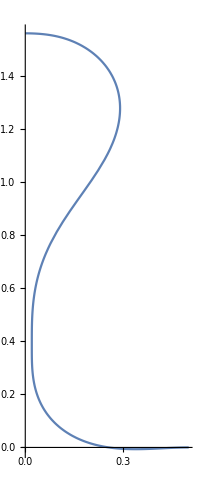

```mathematica
Sol=FindRoot[RodOdeContactRegion[R],{R,R0},AccuracyGoal->6,MaxIterations->Infinity,PrecisionGoal->6];
sol=EquilSolContactRegion[R/.Sol];
ParametricPlot[{x[S],y[S]}/.sol,{S,0,L/2}]
```

```mathematica
Norm[RodOdeContactRegion[R/.Sol]]
```

4.64913×10^-9

```mathematica
R/.Sol
```

{-13.027,1.56028,-3.95468,0.324096,0.328602,5833.8,-87.3043}

```mathematica
g=γ[S]
```

4.30051

#### Contact region

```mathematica
γ[S_]=g;
rs=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* second step *)
dt=0.001;
dth=dt; (* initialising successful dt *)
g=g+dt;
γ[S_]=g;
Sol=FindRoot[RodOdeContactRegion[R],{R,R/.Sol}];
sol=EquilSolContactRegion[R/.Sol];
re=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,re,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];

(* tracing *)
flag=0;
FailCount=0;
TOL=10^-4;
MaxDt=0.15;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)

While[flag==0,
t = (re - rs);
g=g+dt;
γ[S_]=g;

Sol=Quiet[Reap[FindRoot[RodOdeContactRegion[R],{R,re+dt/dth t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOdeContactRegion[R/.Sol[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
g=g-dt;
dt = 0.5 dt; Print[dt];If[FailCount == 200, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSolContactRegion[R/.Sol[[1]]];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol],{S,0,L/2}];
CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 
(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.00125

0.0015625

0.00195313

0.00244141

0.00305176

0.0038147

0.00476837

0.00596046

0.00745058

0.00931323

0.0116415

0.0145519

0.0181899

0.0227374

0.0284217

0.0355271

0.0177636

0.0222045

0.0277556

0.0346945

0.0433681

0.0542101

0.0677626

0.0847033

0.0423516

0.0211758

$Aborted

```mathematica
NotebookClose[J1]
```

```mathematica
Length[grs]
```

313

```mathematica
Save[ToString[$HomeDirectory]<>"/Dropbox/Research (unshared,current)/Morphorods/SelfContact/Lagrangian", grs]
```

```mathematica
grs=Get[ToString[$HomeDirectory]<>"/Dropbox/Research (unshared,current)/Morphorods/SelfContact/Lagrangian"];
```

```mathematica
Manipulate[ParametricPlot[{{-x[S],y[S]}/.grs[[i,6]],{x[S],y[S]}/.grs[[i,6]]},{S,0,1/2},PlotRange->{{-1,1},{-1,2.5}}],{i,1,Length[grs],1}]
```

Part::partd: Part specification grs ⟦ 275, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 275, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 275, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 275, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 275, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 275, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 275, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 275, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 275, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 275, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification Global`grs ⟦ 275, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Global`grs ⟦ 275, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification Global`grs ⟦ 275, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Global`grs ⟦ 275, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification Global`grs ⟦ 275, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification Global`grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Global`grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification Global`grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Global`grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification Global`grs ⟦ 160, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification Global`grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Global`grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification Global`grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Global`grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification Global`grs ⟦ 160, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partw: Part 275 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {10.202149658203126`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {10.202149658203126`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 24 »{10.202149658203126`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 160 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {10.202149658203126`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {10.202149658203126`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 24 »{10.202149658203126`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 275 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 27 », {3.3726562500000004`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 27 », {3.3726562500000004`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 27 »{3.3726562500000004`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 160 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 27 », {3.3726562500000004`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 27 », {3.3726562500000004`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 27 »{3.3726562500000004`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 160 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 35 »{3.670991077423096`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, « 6 », TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 275 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 35 »{3.670991077423096`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, « 6 », TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 160 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 35 »{3.670991077423096`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, « 6 », TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 275 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 35 »{3.670991077423096`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, « 6 », TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 275 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {4.770912109375001`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {4.770912109375001`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 24 »{4.770912109375001`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {4.770912109375001`, « 6 », TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 160 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {4.770912109375001`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {4.770912109375001`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 24 »{4.770912109375001`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {4.770912109375001`, « 6 », TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 275 of {1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 49 »« 183 » does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, {1.1`, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {« 9 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 48 », « 183 »} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 49 »« 183 » does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, {1.1`, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {« 9 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 48 », « 183 »} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 49 »« 183 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, {1.1`, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {« 9 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 48 », « 183 »} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
Manipulate[Plot[{{y[S]}/.grs[[i,6]]},{S,0,1/2},PlotRange-> Full],{i,1,Length[grs],1}]
```

Part::partd: Part specification grs ⟦ 192, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 192, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 192, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ReplaceAll::reps: {grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 192, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 192, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 192, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ReplaceAll::reps: {grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 192, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 192, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 192, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ReplaceAll::reps: {grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification Global`grs ⟦ 192, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Global`grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification Global`grs ⟦ 192, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Global`grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification Global`grs ⟦ 192, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ReplaceAll::reps: {Global`grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 192, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 192, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 192, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ReplaceAll::reps: {grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 192 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {10.202149658203126`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 192 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 24 »{10.202149658203126`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 192 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {10.202149658203126`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 192 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 27 », {3.3726562500000004`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 192 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 27 »{3.3726562500000004`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 192 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 27 », {3.3726562500000004`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 192 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 192 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 35 »{3.670991077423096`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

ReplaceAll::reps: {{1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, « 6 », TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 192 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
Length[grs]
```

369

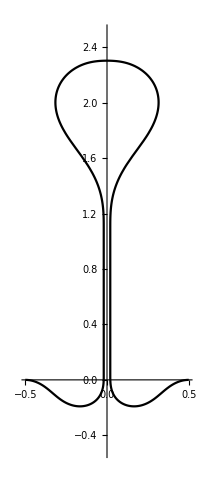

```mathematica
II={10,20,50,80,100,300,340,350,369};
II={369};
For[i=1,i≤Length[II],i++,
Subscript[P, i]=ParametricPlot[{{-x[S],y[S]}/.grs[[II[[i]],6]],{x[S],y[S]}/.grs[[II[[i]],6]]},{S,0,1/2},PlotStyle->{Black,Black}];
];
Show[Table[Subscript[P, k],{k,1,Length[II]}],PlotRange->{{-.5,.5},{-.5,2.5}}]
```

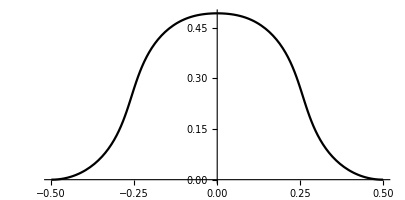

```mathematica
i=10;ParametricPlot[{{-x[S],y[S]}/.grs[[i,6]],{x[S],y[S]}/.grs[[i,6]]},{S,0,1/2},PlotStyle->{Black,Black}]
```

### Heterogeneous stiffness, uniform growth

#### Initial solution, parameters

```mathematica
Clear[γ,R,Sol,sol,EB,px,py];
(* parameters *)
k=50;
dt=0.05;
dth = dt; (* initialising successful step size *)
δ=0.1;
L=1;
η=1;
γ[S_]=1+dt;
px[S_]:=S;
py[S_]:=0;
EB[s_]:=1-.5Exp[-s^2/(.005)];
Sol=FindRoot[RodOde[R],{R,{-42,0.1,-4}}];
Plot[EB[s],{s,0,1/2},PlotRange->{0,1}]
ParametricPlot[Evaluate[{x[S],y[S]}/.EquilSol[R/.Sol]],{S,0,L/2}]
```

-Graphics-

-Graphics-

#### Growth to contact

```mathematica
grs={};
(* first step *)
g=1+dt;
γ[S_]=g;
Sol=FindRoot[RodOde[R],{R,R/.Sol}];
sol=EquilSol[R/.Sol];
rs=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];

(* second step *)
g=g+dt;
γ[s_]=g;
Sol=FindRoot[RodOde[R],{R,R/.Sol}];
sol=EquilSol[R/.Sol];
re=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];

(* tracing *)
flag=0;
FailCount=0;
TOL=10^-6;
MaxDt=0.35;
MaxFails=60;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];
P2=Plot[(x[S]-δ)/.sol,{S,0,L/2}];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
J2 = CreateWindow[DocumentNotebook[P2],WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)

While[flag==0,
t = (re - rs);
g=g+dt;
γ[s_]=g;
Sol=Quiet[Reap[FindRoot[RodOde[R],{R,re+dt/dth*t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOde[R/.Sol[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
g=g-dt;
γ[s_]=g;
dt = 0.5 dt; Print[dt];If[FailCount == MaxFails, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSol[R/.Sol[[1]]];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];

Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];
P2=Plot[(x[S]-δ)/.sol,{S,0,L/2}];
CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 CreateWindow[DocumentNotebook[P2],J2,WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];
(*FinishDynamic[]*);

(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

0.0625

0.078125

0.0976563

0.12207

0.152588

0.190735

$Aborted

```mathematica
NotebookClose[J1];NotebookClose[J2];
```

```mathematica
Manipulate[ParametricPlot[{x[s],y[s]}/.grs[[i,6]],{s,0,grs[[i,2]]/2},PlotRange->All],{i,1,Length[grs],1}]
```

```mathematica
Manipulate[Plot[(x[s]-δ)/.grs[[i,6]],{s,0,L/2}],{i,1,Length[grs],1}]
```

```mathematica
Save[ToString[$HomeDirectory]<>"/Dropbox/Research (unshared,current)/Morphorods/SelfContact/Lagrangian", grs]
```

#### First contact point

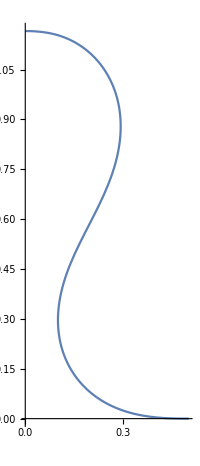

```mathematica
ii=24;
sc=0.33; (* guess for contact location *)
grs=Table[grs[[k]],{k,1,ii}];
γ[S_]=grs[[ii,1]];
R0=grs[[ii,5]];
R0=Flatten[AppendTo[R0,{sc,0}]];
px=grs[[ii,7]];
py=grs[[ii,8]];
Sol=FindRoot[RodOdeContactPt[R],{R,R0}];
sol=EquilSolnContactPt[R/.Sol];
ParametricPlot[{x[S],y[S]}/.sol,{S,0,L/2}]
```

```mathematica
A0=-NIntegrate[x[S]y'[S]/.sol,{S,0,(R/.Sol)[[4]]}]
```

0.182148

```mathematica
rs=Flatten[AppendTo[R/.Sol,0]]
```

Set::write: Tag ReplaceAll in R/.{R→{-7.61589,1.16567,-3.98773,0.328367,0.297195}} is Protected.

{-7.61589,1.16567,-3.98773,0.328367,0.297195,0}

```mathematica
Sol=FindRoot[RodOdeContactPtAreaCons[R],{R,rs}];
sol=EquilSolnContactPtAreaCons[R/.Sol];
```

```mathematica
g=γ[s]
```

3.29105

#### Evolving contact point; Seeking contact region

```mathematica
(* first step done above *)
(*g=3.825;*)
γ[S_]=g;
rs=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* second step *)
dt=0.005;
dth=dt; (* initialising successful dt *)
g=g+dt;
γ[S_]=g;
Sol=FindRoot[RodOdeContactPtAreaCons[R],{R,R/.Sol}];
sol=EquilSolnContactPtAreaCons[R/.Sol];
re=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,re,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* tracing *)
flag=0;
FailCount=0;
TOL=10^-4;
MaxDt=0.15;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];
P2=Plot[m[S]/.sol,{S,0,L/2}];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
J2 = CreateWindow[DocumentNotebook[P2],WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)

While[flag==0,
t = (re - rs);
g=g+dt;
γ[S_]=g;

Sol=Quiet[Reap[FindRoot[RodOdeContactPtAreaCons[R],{R,re+dt/dth t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOdeContactPtAreaCons[R/.Sol[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
g=g-dt;
dt = 0.5 dt; Print[dt];If[FailCount == 100, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSolnContactPtAreaCons[R/.Sol[[1]]];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol],{S,0,L/2}];
P2=Plot[m[S]/.sol,{S,0,L/2}];
 CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 CreateWindow[DocumentNotebook[P2],J2,WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];
(*FinishDynamic[]*)

(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

$Aborted

```mathematica
NotebookClose[J1];NotebookClose[J2];
```

```mathematica
ii=27;
```

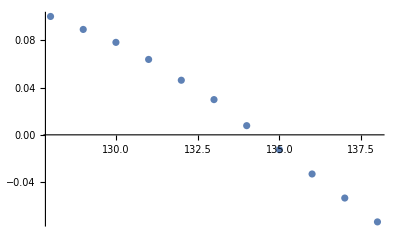

```mathematica
ListPlot[Table[{i,m[S]/.grs[[i,6]]/.S->grs[[i,5,4]]},{i,128,Length[grs]}]]
```

```mathematica
Save[ToString[$HomeDirectory]<>"/Dropbox/Research (unshared,current)/Morphorods/SelfContact/Lagrangian", grs]
```

```mathematica
grs=Get[ToString[$HomeDirectory]<>"/Dropbox/Research (unshared,current)/Morphorods/SelfContact/Lagrangian"];
```

```mathematica
Manipulate[ParametricPlot[{{-x[S],y[S]}/.grs[[i,6]],{x[S],y[S]}/.grs[[i,6]]},{S,0,L/2},PlotRange->All,PlotStyle->{Blue,Blue}],{i,1,Length[grs],1}]
Manipulate[Plot[m[S]/.grs[[i,6]],{S,0,L/2}],{i,1,Length[grs],1}]
```

#### First contact region solution

```mathematica
Length[grs]
```

225

```mathematica
ii=135;
m[S]/.grs[[ii,6]]/.S->grs[[ii,5,4]]
grs=Table[grs[[k]],{k,1,ii}];
```

-0.0125873

```mathematica
A0
```

0.206189

```mathematica
(*A0=0.20618879019655859;*)
γ[S_]=grs[[ii,1]];
px=grs[[ii,7]];
py=grs[[ii,8]];
R0=grs[[ii,5]];
eps=0.01;
R0={R0[[1]],R0[[2]],R0[[3]],R0[[4]]-eps,R0[[4]]+eps,R0[[5]]/2/eps,R0[[6]]};
```

```mathematica
RodOdeContactRegion[R0]
```

{0.000623752,-0.00682961,0.29876,-0.00319619,-0.00919894,-0.00487466,0.0505482}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

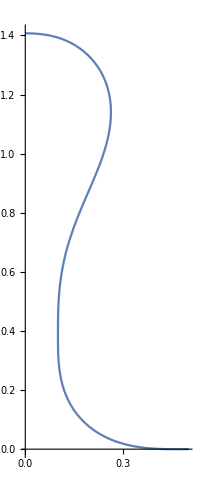

```mathematica
Sol=FindRoot[RodOdeContactRegion[R],{R,R0},AccuracyGoal->6,MaxIterations->Infinity,PrecisionGoal->6];
sol=EquilSolContactRegion[R/.Sol];
ParametricPlot[{x[S],y[S]}/.sol,{S,0,L/2}]
```

```mathematica
Norm[RodOdeContactRegion[R/.Sol]]
```

0.0000765583

```mathematica
R/.Sol
```

{-17.1415,1.40709,-4.61163,0.32312,0.323583,57983.4,-98.3801}

```mathematica
g=γ[S]
```

3.71439

#### Contact region

```mathematica
γ[S_]=g;
rs=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* second step *)
dt=0.001;
dth=dt; (* initialising successful dt *)
g=g+dt;
γ[S_]=g;
Sol=FindRoot[RodOdeContactRegion[R],{R,R/.Sol}];
sol=EquilSolContactRegion[R/.Sol];
re=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,re,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];

(* tracing *)
flag=0;
FailCount=0;
TOL=10^-4;
MaxDt=0.15;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)

While[flag==0,
t = (re - rs);
g=g+dt;
γ[S_]=g;

Sol=Quiet[Reap[FindRoot[RodOdeContactRegion[R],{R,re+dt/dth t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOdeContactRegion[R/.Sol[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
g=g-dt;
dt = 0.5 dt; Print[dt];If[FailCount == 200, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSolContactRegion[R/.Sol[[1]]];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol],{S,0,L/2}];
CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 
(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

$Aborted

```mathematica
NotebookClose[J1]
```

```mathematica
Length[grs]
```

343

```mathematica
Length[grs]
```

343

```mathematica
II={2,10,18,50,260,300,325,343};
For[i=1,i≤Length[II],i++,
Subscript[P, i]=ParametricPlot[{{-x[S],y[S]}/.grs[[II[[i]],6]],{x[S],y[S]}/.grs[[II[[i]],6]]},{S,0,1/2},PlotStyle->{Black,Black}];
];
```

```mathematica
Show[Table[Subscript[P, k],{k,1,Length[II]}],PlotRange->{{-.5,.5},{-.5,3}},AspectRatio->8,ImageSize->80]
```

-Graphics-

```mathematica
Grs=Table[grs[[II[[i]]]],{i,1,Length[II]}];
```

```mathematica
Save[ToString[$HomeDirectory]<>"/Dropbox/Research (unshared,current)/Morphorods/SelfContact/Lagrangian2", Grs]
```

```mathematica
Grs=Get[ToString[$HomeDirectory]<>"/Dropbox/Research (unshared,current)/Morphorods/SelfContact/Lagrangian"];
```

```mathematica
Manipulate[ParametricPlot[{{-x[S],y[S]}/.Grs[[i,6]],{x[S],y[S]}/.Grs[[i,6]]},{S,0,1/2},PlotRange->{{-1,1},{-1,3}},AspectRatio->5],{i,1,Length[Grs],1}]
```

### Heterogeneous stiffness, homogeneous growth, horizontal repulsion

-Graphics-

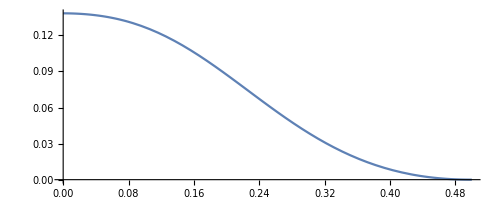

```mathematica
Clear[γ,R,Sol,sol,EB,px,py];
(* parameters *)
k=50;
dt=0.05;
dth = dt; (* initialising successful step size *)
δ=0.02;
L=1;
η=1;
γ[S_]=1+dt;
px[S_]:=S;
py[S_]:=0;
Q = 10.0;
n= 2.0;
EB[s_]:=1-.5Exp[-s^2/(.005)];
Sol=FindRoot[RodOdeRepulsion[R],{R,{-42,0.1,-4}}];
Plot[EB[s],{s,0,1/2},PlotRange->{0,1}]
ParametricPlot[Evaluate[{x[S],y[S]}/.EquilSolRepulsion[R/.Sol]],{S,0,L/2}]
```

#### Growth to self-contact

```mathematica
grs={};
(* first step *)
g=1+dt;
γ[S_]=g;
Sol=FindRoot[RodOdeRepulsion[R],{R,R/.Sol}];
sol=EquilSolRepulsion[R/.Sol];
rs=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];

(* second step *)
g=g+dt;
γ[s_]=g;
Sol=FindRoot[RodOdeRepulsion[R],{R,R/.Sol}];
sol=EquilSolRepulsion[R/.Sol];
re=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];

(* tracing *)
flag=0;
FailCount=0;
TOL=10^-6;
MaxDt=0.35;
MaxFails=60;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];
P2=Plot[(x[S]-δ)/.sol,{S,0,L/2}];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
J2 = CreateWindow[DocumentNotebook[P2],WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)
rd
While[flag==0,
t = (re - rs);
g=g+dt;
γ[s_]=g;
Sol=Quiet[Reap[FindRoot[RodOdeRepulsion[R],{R,re+dt/dth*t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOdeRepulsion[R/.Sol[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
g=g-dt;
γ[s_]=g;
dt = 0.5 dt; Print[dt];If[FailCount == MaxFails, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSolRepulsion[R/.Sol[[1]]];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];

Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];
P2=Plot[(x[S]-δ)/.sol,{S,0,L/2}];
CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 CreateWindow[DocumentNotebook[P2],J2,WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];
(*FinishDynamic[]*);

(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

rd

0.0625

0.078125

0.0976563

0.12207

0.0610352

$Aborted

```mathematica
NotebookClose[J1];NotebookClose[J2];
```

```mathematica
Manipulate[ParametricPlot[{x[s],y[s]}/.grs[[i,6]],{s,0,grs[[i,2]]/2},PlotRange->All],{i,1,Length[grs],1}]
```

```mathematica
Manipulate[Plot[{x[s]-δ}/.grs[[i,6]],{s,0,grs[[i,2]]/2},PlotRange->All],{i,1,Length[grs],1}]
```

```mathematica
dth
```

0.152588

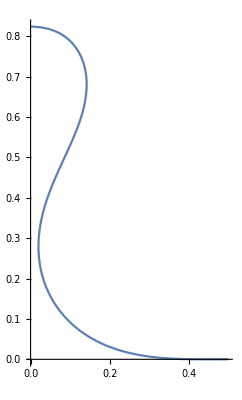

```mathematica
ii=23;
sc=0.26; (* guess for contact location *)
grs=Table[grs[[k]],{k,1,ii}];
γ[S_]=grs[[ii,1]];
R0=grs[[ii,5]];
R0=Flatten[AppendTo[R0,{sc,0}]];
px=grs[[ii,7]];
py=grs[[ii,8]];
Sol=FindRoot[RodOdeContactPtRepulsion[R],{R,R0}];
sol=EquilSolnContactPtRepulsion[R/.Sol];
ParametricPlot[{x[S],y[S]}/.sol,{S,0,L/2}]
```

```mathematica
ii
```

23

```mathematica
g=γ[S]
```

2.56328

### Seeking contact region

```mathematica
g=γ[S];
rs=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* second step *)
dt=0.05;
dth=dt; (* initialising successful dt *)
g=g+dt;
γ[S_]=g;
Sol=FindRoot[RodOdeContactPtRepulsion[R],{R,R/.Sol}];
sol=EquilSolnContactPtRepulsion[R/.Sol];
re=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,re,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* tracing *)
flag=0;
FailCount=0;
TOL=10^-4;
MaxDt=0.15;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];
P2=Plot[m[S]/.sol,{S,0,L/2}];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
J2 = CreateWindow[DocumentNotebook[P2],WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)

While[flag==0,
t = (re - rs);
g=g+dt;
γ[S_]=g;

Sol=Quiet[Reap[FindRoot[RodOdeContactPtRepulsion[R],{R,re+dt/dth t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOdeContactPtRepulsion[R/.Sol[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
g=g-dt;
dt = 0.5 dt; Print[dt];If[FailCount == 100, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSolnContactPtRepulsion[ R/.Sol[[1]]];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol],{S,0,L/2}];
P2=Plot[m[S]/.sol,{S,0,L/2}];
 CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 CreateWindow[DocumentNotebook[P2],J2,WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];
(*FinishDynamic[]*)

(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

0.0625

0.078125

$Aborted

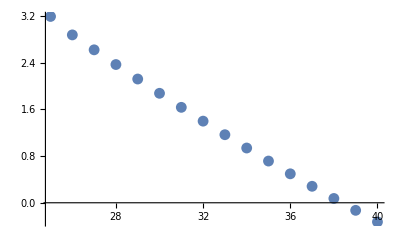

$Aborted

```mathematica
ListPlot[Table[{i,m[S]/.grs[[i,6]]/.S->grs[[i,5,4]]},{i,25,40}]]
```

```mathematica
Manipulate[ParametricPlot[{{-x[S],y[S]}/.grs[[i,6]],{x[S],y[S]}/.grs[[i,6]]},{S,0,L/2},PlotRange->All,PlotStyle->{Blue,Blue}],{i,1,Length[grs],1}]
Manipulate[Plot[m[S]/.grs[[i,6]],{S,0,L/2}],{i,1,Length[grs],1}]
```

### Contact along a region

```mathematica
ii=39;
m[S]/.grs[[ii,6]]/.S->grs[[ii,5,4]]
grs=Table[grs[[k]],{k,1,ii}];
```

-0.129697

```mathematica
γ[S_]=grs[[ii,1]];
px=grs[[ii,7]];
py=grs[[ii,8]];
R0=grs[[ii,5]];
eps=0.01;
R0={R0[[1]],R0[[2]],R0[[3]],R0[[4]]-eps,R0[[4]]+eps,R0[[5]]/2/eps};
```

```mathematica
R0
```

{-42.3585,1.15867,-9.06317,0.272194,0.292194,1780.29}

3.7209

```mathematica
RodOdeContactPtRepulsion[R0]
```

{-0.00188179,-0.021442,-0.937592,0.00663964,-3.51851}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

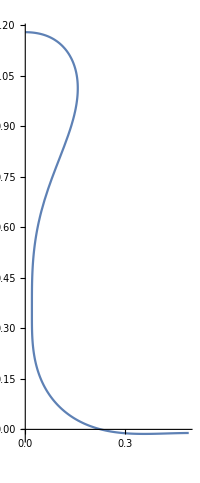

```mathematica
Sol=FindRoot[RodOdeContactRegionRepulsion[R],{R,R0},AccuracyGoal->6,MaxIterations->Infinity,PrecisionGoal->6];
sol=EquilSolContactRegionRepulsion[R/.Sol];
ParametricPlot[{x[S],y[S]}/.sol,{S,0,L/2}]
```

```mathematica
g=γ[S]
```

3.31328

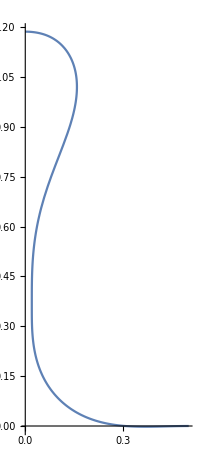

```mathematica
γ[S_]=g;
rs=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* second step *)
dt=0.001;
dth=dt; (* initialising successful dt *)
g=g+dt;
γ[S_]=g;
Sol=FindRoot[RodOdeContactRegionRepulsion[R],{R,R/.Sol}];
sol=EquilSolContactRegionRepulsion[R/.Sol];
re=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,re,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
ParametricPlot[{x[S],y[S]}/.sol,{S,0,L/2}]
```

```mathematica
dth
```

0.001

```mathematica
(* tracing *)
flag=0;
FailCount=0;
TOL=10^-4;
MaxDt=0.15;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)

While[flag==0,
t = (re - rs);
g=g+dt;
γ[S_]=g;

Sol=Quiet[Reap[FindRoot[RodOdeContactRegionRepulsion[R],{R,re+dt/dth t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOdeContactRegionRepulsion[R/.Sol[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
g=g-dt;
dt = 0.5 dt; Print[dt];If[FailCount == 200, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSolContactRegionRepulsion[R/.Sol[[1]]];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol],{S,0,L/2}];
CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 
(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

0.00155575

0.00194469

Part::partw: Part 1 of {} does not exist.

0.00243087

0.00303858

0.00151929

0.000759645

Part::partw: Part 1 of {} does not exist.

0.000949557

0.00118695

0.00148368

0.0018546

0.00231825

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

0.00289782

0.00362227

0.00452784

0.0056598

0.0028299

0.00353737

0.00442172

0.00221086

0.00276357

0.00345447

0.00431808

0.00539761

0.00674701

0.0033735

0.00421688

0.00210844

0.00105422

0.00131777

0.00164722

0.00205902

0.00257378

0.00321722

0.00160861

0.000804306

0.000402153

0.000201076

0.000251346

0.000314182

0.000392727

$Aborted

```mathematica
γ[S]
```

5.06638

```mathematica
dth
```

0.000314182

```mathematica
NotebookClose[J1]
Length[grs]
```

453

```mathematica
II={2,10,18,35, 45, 150, 200, 250, 300, 350, 400, 453};
For[i=1,i≤Length[II],i++,
Subscript[P, i]=ParametricPlot[{{-x[S],y[S]}/.grs[[II[[i]],6]],{x[S],y[S]}/.grs[[II[[i]],6]]},{S,0,1/2},PlotStyle->{Black,Black}];
];
```

```mathematica
Show[Table[Subscript[P, k],{k,1,Length[II]}],PlotRange->{{-.5,.5},{-.5,3}},AspectRatio->8,ImageSize->80]
```

-Graphics-

```mathematica
Grs=Table[grs[[II[[i]]]],{i,1,Length[II]}];
```

```mathematica
Save[ToString[$HomeDirectory]<>"/Documents/MorphoCrypt/Mathematica/SelfContact/", Grs]
```

```mathematica
Manipulate[ParametricPlot[{{-x[S],y[S]}/.Grs[[i,6]],{x[S],y[S]}/.Grs[[i,6]]},{S,0,1/2},PlotRange->{{-1,1},{-1,3}},AspectRatio->5],{i,1,Length[Grs],1}]
```

Part::partd: Part specification Grs ⟦ 7, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Grs ⟦ 7, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification Grs ⟦ 7, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Grs ⟦ 7, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification Grs ⟦ 7, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.